## Lagrange Interpolation

```mathematica
laGrange[dataPoints_]:=Module[{n = Length[dataPoints]},
Return[∑_(j=1)^n (dataPoints⟦j,2⟧*(∏_(k=1)^(j-1) (x - dataPoints⟦k,1⟧)/(dataPoints⟦j,1⟧-dataPoints⟦k,1⟧))*(∏_(k=j+1)^n (x - dataPoints⟦k,1⟧)/(dataPoints⟦j,1⟧-dataPoints⟦k,1⟧)))];
]
```

```mathematica
points = List[{1,1},{2,4},{3,9},{4,16},{5,25}];
```

```mathematica
laGrange[points]
```

1/24 (2-x) (3-x) (4-x) (5-x)+2/3 (3-x) (4-x) (5-x) (-1+x)+9/4 (4-x) (5-x) (-2+x) (-1+x)+8/3 (5-x) (-3+x) (-2+x) (-1+x)+25/24 (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Simplify[1/24 (2-x) (3-x) (4-x) (5-x)+2/3 (3-x) (4-x) (5-x) (-1+x)+9/4 (4-x) (5-x) (-2+x) (-1+x)+8/3 (5-x) (-3+x) (-2+x) (-1+x)+25/24 (-4+x) (-3+x) (-2+x) (-1+x)]
```

x^2

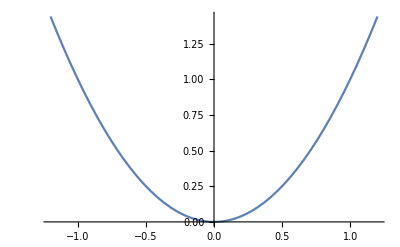

```mathematica
Plot[x^2,{x,-1.2,1.2}]
```